```mathematica
(*参数设置*)
Clear[θ1,θ2];
g=10;(*重力加速度*)
l1=1;l2=1;(*摆长*)
m1=1;m2=1;(*小球质量*)
θ1i=Pi/180*0;θ2i=Pi/180*90;(*初始条件*)
x1=l1*Sin[θ1[t]];
y1=l1*Cos[θ1[t]];(*注意y1和y2取负方向，因此势能要加负号,最终绘图也要加负号*)
x2=x1+l2*Sin[θ2[t]];
y2=y1+l2*Cos[θ2[t]];
x1p=D[x1,t];
y1p=D[y1,t];
x2p=D[x2,t];
y2p=D[y2,t];
L=1/2 m1(x1p^2+y1p^2)+1/2 m2(x2p^2+y2p^2)+m1*g*y1+m2*g*y2;
```

```mathematica
(*生成演化方程*)
eq1=D[L,θ1[t]]==D[D[L,θ1'[t]],t];
eq2=D[L,θ2[t]]==D[D[L,θ2'[t]],t];
θ1v=0;θ2v=0;(*初始角速度*)
```

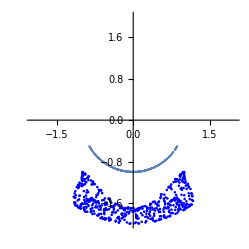

```mathematica
sol=NDSolve[{
eq1,
eq2,
θ1[0]==θ1i,
θ2[0]==θ2i,
θ1'[0]==θ1v,
θ2'[0]==θ2v

},{θ1,θ2},{t,0,9000}];
(*赋值*)
θ1r=θ1/.sol[[1]];
θ2r=θ2/.sol[[1]];
(*画图(x1,-y1)与(x2,-y2)*)
data1=Table[{l1*Sin[θ1r[t]],-l1*Cos[θ1r[t]]},{t,0,50,0.1}];
data2=Table[{l1*Sin[θ1r[t]]+l2*Sin[θ2r[t]],-l1*Cos[θ1r[t]]-l2*Cos[θ2r[t]]},{t,0,50,0.1}];
ListPlot[data1,AspectRatio->1,PlotRange->{{-l1-l2,l1+l2},{-l1-l2,l1+l2}}]~Show~ListPlot[data2,AspectRatio->1,PlotRange->{{-l1-l2,l1+l2},{-l1-l2,l1+l2}},PlotStyle->Blue]
```

```mathematica
data0=Table[{0,0},Length[data1]];
flash=Table[ListLinePlot[Partition[Transpose[{Transpose[{data0,data1}],data2}][[i]]//Flatten,2],AspectRatio->1,PlotRange->{{-l1-l2,l1+l2},{-l1-l2,l1+l2}},PlotStyle->Blue],{i,1,Length[data1]}];
```

```mathematica
Manipulate[flash[[i]],{i,1,Length[data1],1}]
```